# Chi4

## data loading

```mathematica
p0s={3.85,3.825,3.80,3.775,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{2, 4,10, 20, 40,60, 80, 200, 500, 800, 1400, 2500, 4200,5000, 6000, 8500, 9500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{1, 3, 4 ,8 ,15,40 ,70 ,150 ,250, 600 ,2000, 2500 ,4500, 9500},{2, 10,20 ,30, 80 ,100 ,400 ,500 ,2500 ,2500, 3000 ,7000, 10000},{4 ,5 ,7 ,10 ,30 ,70, 150 ,700,1400, 4000 ,9500}};
```

```mathematica
overlapCRoverlap=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/overlapCRoverlap_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/overlapCRoverlap_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/overlapCRoverlap_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/overlapCRoverlap_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
SISFCRSISF=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/SISFCRSISF_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/SISFCRSISF_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/SISFCRSISF_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/SISFCRSISF_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
CRoverlapVar=Table[Table[Table[Variance[DeleteCases[Table[overlapCRoverlap[[p,T,i,2,rec]],{i,Length[overlapCRoverlap[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[overlapCRoverlap[[p,T,i,1]]],{i,Length[overlapCRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
overlapVar=Table[Table[Table[Variance[DeleteCases[Table[overlapCRoverlap[[p,T,i,1,rec]],{i,Length[overlapCRoverlap[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[overlapCRoverlap[[p,T,i,1]]],{i,Length[overlapCRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRSISFVar=Table[Table[Table[Variance[DeleteCases[Table[SISFCRSISF[[p,T,i,2,rec]],{i,Length[SISFCRSISF[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[SISFCRSISF[[p,T,i,2]]],{i,Length[SISFCRSISF[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
SISFVar=Table[Table[Table[Variance[DeleteCases[Table[SISFCRSISF[[p,T,i,1,rec]],{i,Length[SISFCRSISF[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[SISFCRSISF[[p,T,i,1]]]-3,{i,Length[SISFCRSISF[[p,T]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
time={0.,0.00999999999476131,0.01999999998952262,0.02999999998428393,0.03999999997904524,0.04999999997380655,0.05999999996856786,0.06999999996332917,0.07999999995809048,0.0899999999528518,0.0999999999476131,0.10999999994237442,0.12999999993189704,0.13999999992665835,0.15999999991618097,0.1799999999057036,0.1999999998952262,0.21999999988474883,0.24999999986903276,0.2799999998533167,0.31999999983236194,0.34999999981664587,0.3999999997904524,0.449999999764259,0.4999999997380655,0.5599999997066334,0.6299999996699626,0.709999999628053,0.7899999995861435,0.8899999995337566,0.999999999476131,1.1199999994132668,1.2599999993399251,1.4099999992613448,1.579999999172287,1.7799999990675133,1.999999998952262,2.2399999988265336,2.509999998685089,2.8199999985226896,3.159999998344574,3.5499999981402652,3.9799999979150016,4.469999997658306,5.009999997375417,5.6199999970558565,6.309999996694387,7.079999996291008,7.9399999958404806,8.909999995332328,9.99999999476131,11.21999999412219,12.58999999340449,14.129999992597732,15.849999991696677,17.77999999068561,19.949999989548814,22.389999988270574,25.119999986840412,28.179999985237373,31.619999983435264,35.47999998141313,39.80999997914478,44.669999976598774,50.11999997374369,56.22999997054285,63.09999996694387,70.78999996291532,79.42999995838909,89.12999995330756,99.9999999476131,112.1999999412219,125.88999993405014,141.2499999260035,158.489999916972,177.82999990684038,199.52999989547243,223.86999988272146,251.18999986840936,281.8399998523528,316.2299998343369,354.80999981412606,398.10999979144253,446.6799997659982,501.1899997374421,562.3399997054075,630.9599996694596,707.949999629127,794.3299995838752,891.2499995331018,999.999999476131,1122.0199994122086,1258.9299993404857,1412.5399992600142,1584.8899991697253,1778.2799990684143,1995.2599989547452,2238.719998827204,2511.889998684099,2818.3799985235382,3162.2799983433797,3548.129998141245,3981.069997914441,4466.839997659961,5011.869997374437,5623.40999705407,6309.569996694612,7079.459996291291,7943.279995838762,8912.509995331013,9999.99999476131,11220.179994122096,12589.249993404883,14125.379992600152,15848.929991697238,17782.78999068415,19952.619989547442,22387.209988272036,25118.85998684101,28183.829985235367,31622.779984235283,35481.33998782885,39810.7199918609,44668.35999638493,50118.72000146097,56234.13000715639,63095.73001354675,70794.58002071686,79432.82002876185,89125.09003778848,100000.00004791653}
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

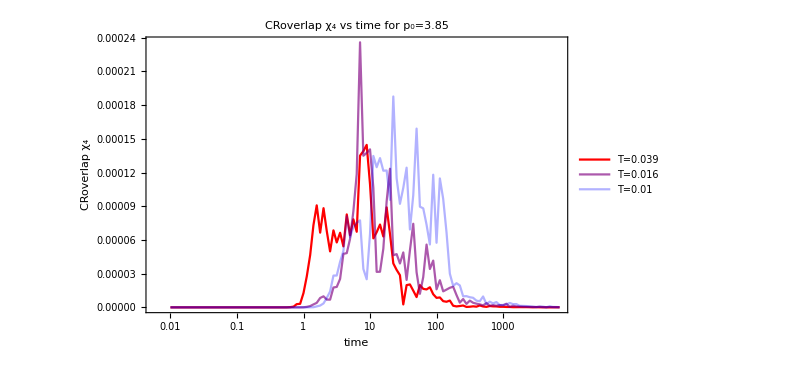
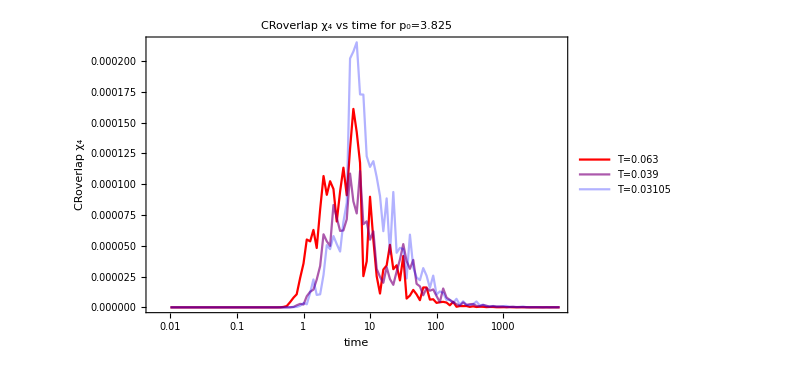
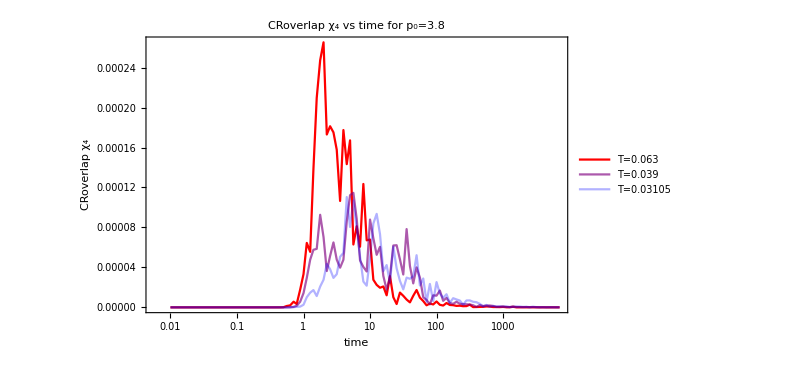
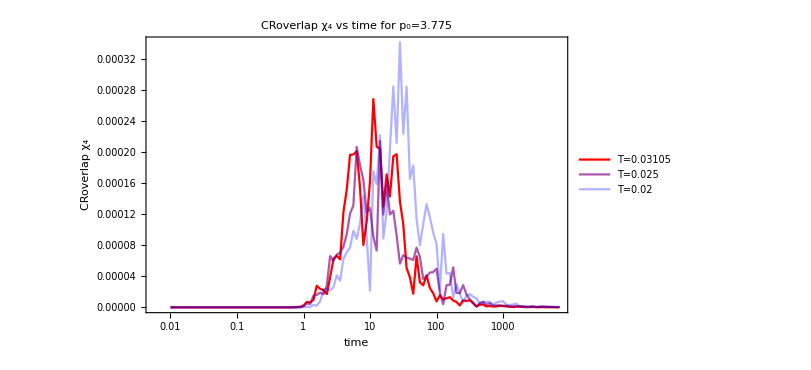
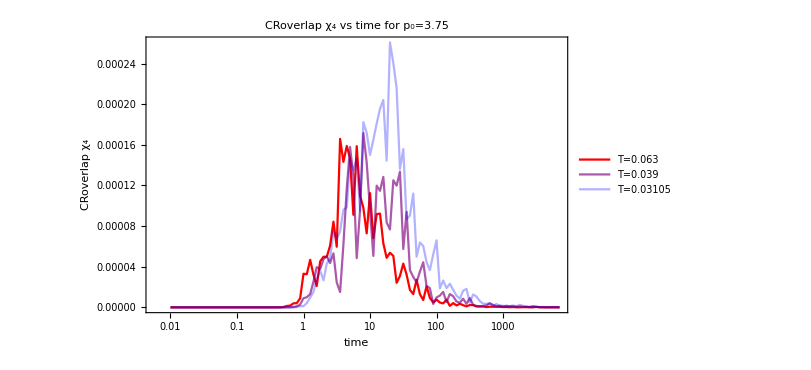

```mathematica
CRoverlapPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapVar[[p,T,rec]]},{rec,Length[CRoverlapVar[[p,T]]]}],{T,3}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->redBluePlotConfig[3],FrameLabel->{"time","CRoverlap χ_4"},ImageSize->600,PlotLabel->"CRoverlap χ_4 vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[CRoverlapPlots]
```

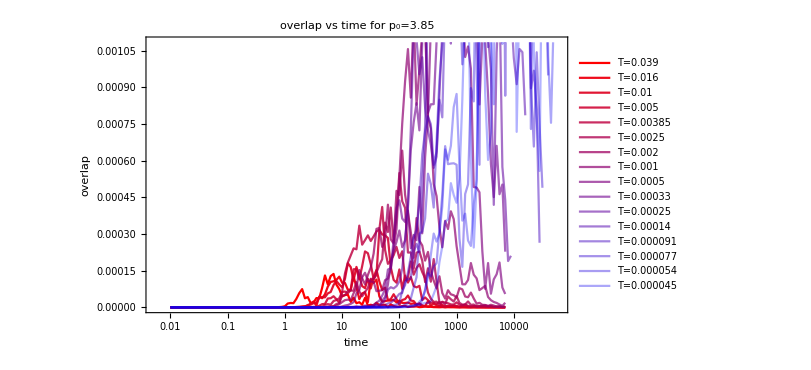
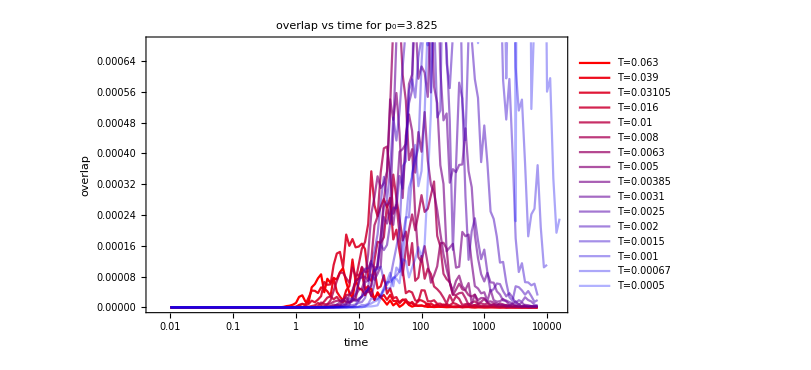
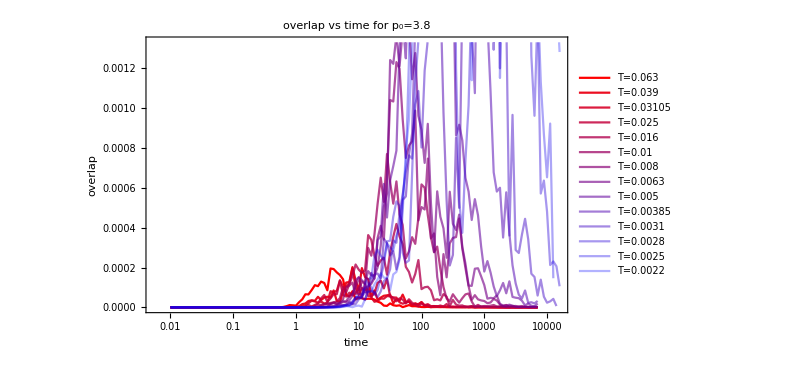
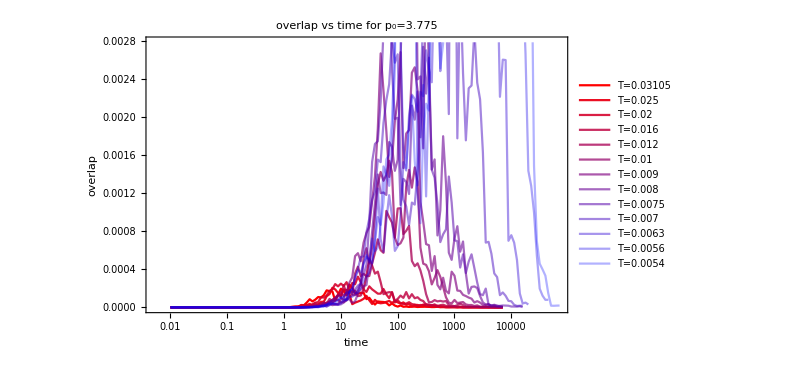
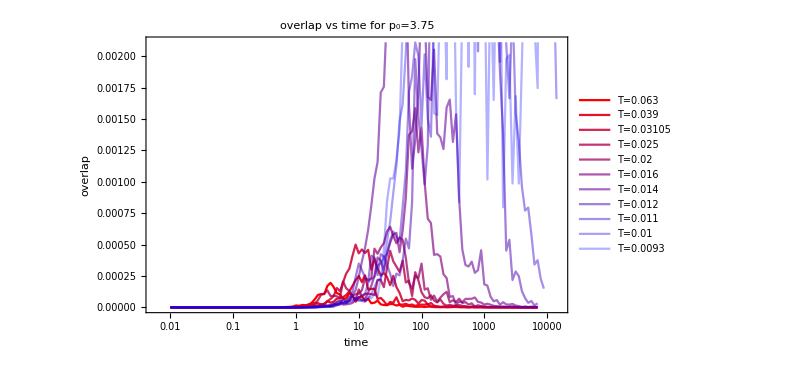

```mathematica
overlapPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],overlapVar[[p,T,rec]]},{rec,Length[overlapVar[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[overlapPlots]
```

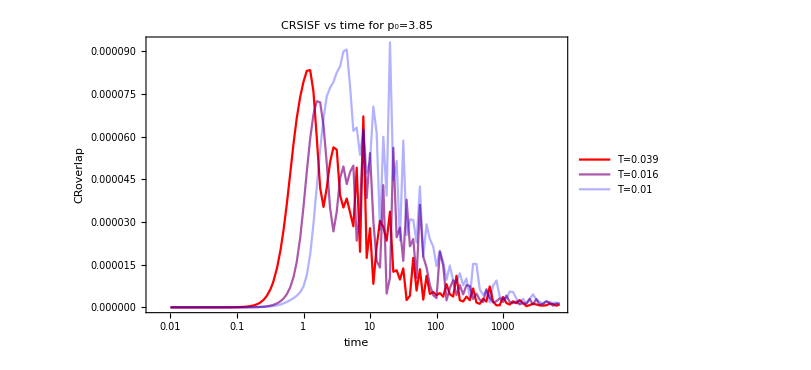
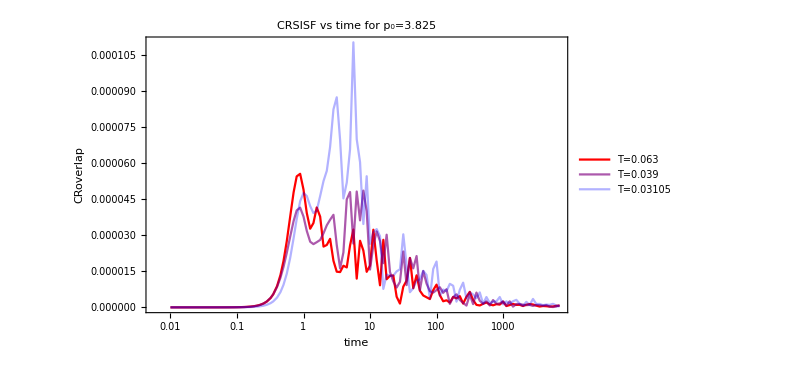
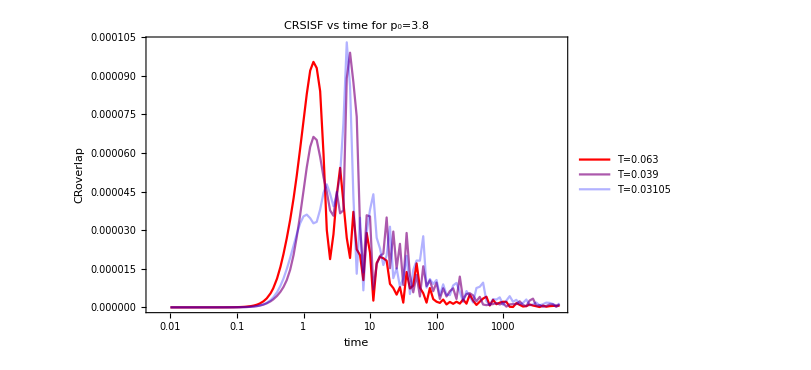
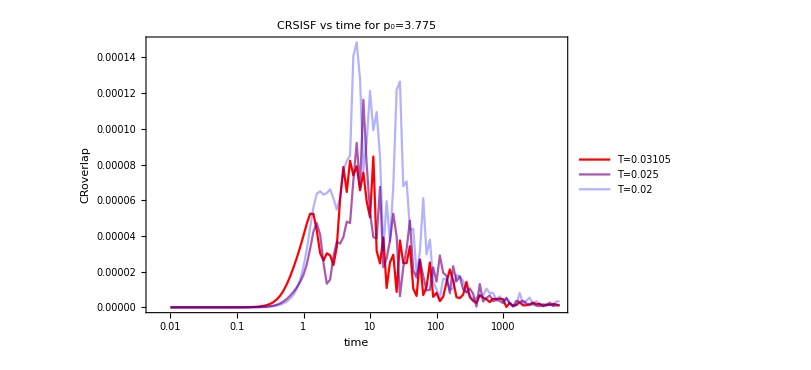
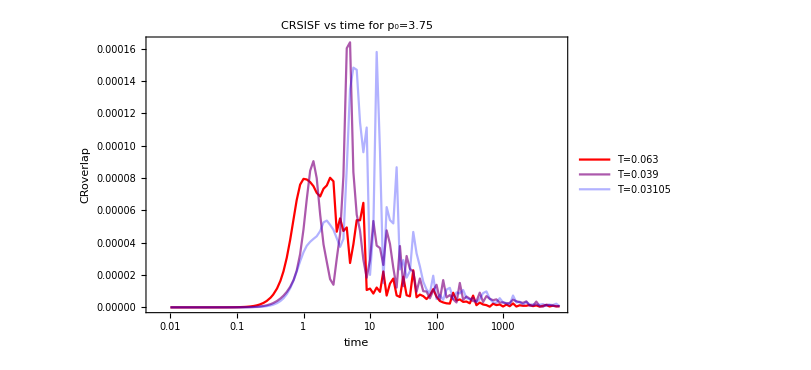

```mathematica
CRSISFPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRSISFVar[[p,T,rec]]},{rec,Length[CRSISFVar[[p,T]]]}],{T,3}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->redBluePlotConfig[3],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[CRSISFPlots]
```

## 3.825 with 200 configurations

```mathematica
p0s={3.825};
```

```mathematica
temperatures={{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015}};
 records={{0,1,2,3,4,5,6,7,8,9}};
tauEstimate={{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000}};
```

```mathematica
CRoverlap=Table[Table[DeleteCases[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/chi4/timeCROverlap_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]*10<1000,1000,tauEstimate[[p,T]]*10]+1000*offset,records[[p,i]]},{3,4,8,0,0}],"Data"],{offset,0,18}],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
neighborOverlap=Table[Table[DeleteCases[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/chi4/neighborOverlap/timeNeighborOverlap_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]*10<1000,1000,tauEstimate[[p,T]]*10]+1000*offset,records[[p,i]]},{3,4,8,0,0}],"Data"],{offset,0,18}],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
CRoverlapVar=Table[Table[Table[Variance[DeleteCases[Flatten[Table[Table[CRoverlap[[p,T,i,offset,2,rec]],{i,Length[CRoverlap[[p,T]]]}],{offset,19}]],_Missing|_Part]],{rec,Max[Table[Length[CRoverlap[[p,T,i,1,1]]],{i,Length[CRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 98 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRoverlapVarSpacing5=Table[Table[Table[Variance[DeleteCases[Flatten[Table[Table[CRoverlap[[p,T,i,offset,2,rec]],{i,Length[CRoverlap[[p,T]]]}],{offset,1,19,5}]],_Missing|_Part]],{rec,Max[Table[Length[CRoverlap[[p,T,i,1,1]]],{i,Length[CRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 105 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRoverlapVarSpacing2=Table[Table[Table[Variance[DeleteCases[Flatten[Table[Table[CRoverlap[[p,T,i,offset,2,rec]],{i,Length[CRoverlap[[p,T]]]}],{offset,1,19,2}]],_Missing|_Part]],{rec,Max[Table[Length[CRoverlap[[p,T,i,1,1]]],{i,Length[CRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 98 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRoverlapVarSpacing3=Table[Table[Table[Variance[DeleteCases[Flatten[Table[Table[CRoverlap[[p,T,i,offset,2,rec]],{i,Length[CRoverlap[[p,T]]]}],{offset,1,19,3}]],_Missing|_Part]],{rec,Max[Table[Length[CRoverlap[[p,T,i,1,1]]],{i,Length[CRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 98 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRoverlapVarSpacing9=Table[Table[Table[Variance[DeleteCases[Flatten[Table[Table[CRoverlap[[p,T,i,offset,2,rec]],{i,Length[CRoverlap[[p,T]]]}],{offset,1,19,9}]],_Missing|_Part]],{rec,Max[Table[Length[CRoverlap[[p,T,i,1,1]]],{i,Length[CRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 98 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
neighborOverlapVar=Table[Table[Table[Variance[DeleteCases[Flatten[Table[Table[neighborOverlap[[p,T,i,offset,2,rec]],{i,Length[neighborOverlap[[p,T]]]}],{offset,19}]],_Missing|_Part]],{rec,Max[Table[Length[neighborOverlap[[p,T,i,1,1]]],{i,Length[neighborOverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 98 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
neighborOverlap[[1,1,1,1,1]]
```

NumericArray[…]

```mathematica
overlap=Table[Table[DeleteCases[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/chi4/timeOverlap_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]*10<1000,1000,tauEstimate[[p,T]]*10]+1000*offset,records[[p,i]]},{3,4,8,0,0}],"Data"],{offset,0,18}],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
overlapVar=Table[Table[Table[Variance[DeleteCases[Flatten[Table[Table[overlap[[p,T,i,offset,2,rec]],{i,Length[overlap[[p,T]]]}],{offset,19}]],_Missing|_Part]],{rec,Max[Table[Length[overlap[[p,T,i,1,1]]],{i,Length[overlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 98 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRSISF=Table[Table[DeleteCases[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/chi4/timeCRSISF_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]*10<1000,1000,tauEstimate[[p,T]]*10]+1000*offset,records[[p,i]]},{3,4,8,0,0}],"Data"],{offset,0,18}],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
CRSISFVar=Table[Table[Table[Variance[DeleteCases[Flatten[Table[Table[CRSISF[[p,T,i,offset,2,rec]],{i,Length[CRSISF[[p,T]]]}],{offset,19}]],_Missing|_Part]],{rec,Max[Table[Length[CRSISF[[p,T,i,1,1]]],{i,Length[CRSISF[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 98 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
SISF=Table[Table[DeleteCases[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/chi4/timeSISF_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]*10<1000,1000,tauEstimate[[p,T]]*10]+1000*offset,records[[p,i]]},{3,4,8,0,0}],"Data"],{offset,0,18}],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
SISFVar=Table[Table[Table[Variance[DeleteCases[Flatten[Table[Table[SISF[[p,T,i,offset,2,rec]],{i,Length[SISF[[p,T]]]}],{offset,19}]],_Missing|_Part]],{rec,Max[Table[Length[SISF[[p,T,i,1,1]]],{i,Length[SISF[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 98 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
time={0.,0.00999999999476131,0.01999999998952262,0.02999999998428393,0.03999999997904524,0.04999999997380655,0.05999999996856786,0.06999999996332917,0.07999999995809048,0.0899999999528518,0.0999999999476131,0.10999999994237442,0.12999999993189704,0.13999999992665835,0.15999999991618097,0.1799999999057036,0.1999999998952262,0.21999999988474883,0.24999999986903276,0.2799999998533167,0.31999999983236194,0.34999999981664587,0.3999999997904524,0.449999999764259,0.4999999997380655,0.5599999997066334,0.6299999996699626,0.709999999628053,0.7899999995861435,0.8899999995337566,0.999999999476131,1.1199999994132668,1.2599999993399251,1.4099999992613448,1.579999999172287,1.7799999990675133,1.999999998952262,2.2399999988265336,2.509999998685089,2.8199999985226896,3.159999998344574,3.5499999981402652,3.9799999979150016,4.469999997658306,5.009999997375417,5.6199999970558565,6.309999996694387,7.079999996291008,7.9399999958404806,8.909999995332328,9.99999999476131,11.21999999412219,12.58999999340449,14.129999992597732,15.849999991696677,17.77999999068561,19.949999989548814,22.389999988270574,25.119999986840412,28.179999985237373,31.619999983435264,35.47999998141313,39.80999997914478,44.669999976598774,50.11999997374369,56.22999997054285,63.09999996694387,70.78999996291532,79.42999995838909,89.12999995330756,99.9999999476131,112.1999999412219,125.88999993405014,141.2499999260035,158.489999916972,177.82999990684038,199.52999989547243,223.86999988272146,251.18999986840936,281.8399998523528,316.2299998343369,354.80999981412606,398.10999979144253,446.6799997659982,501.1899997374421,562.3399997054075,630.9599996694596,707.949999629127,794.3299995838752,891.2499995331018,999.999999476131,1122.0199994122086,1258.9299993404857,1412.5399992600142,1584.8899991697253,1778.2799990684143,1995.2599989547452,2238.719998827204,2511.889998684099,2818.3799985235382,3162.2799983433797,3548.129998141245,3981.069997914441,4466.839997659961,5011.869997374437,5623.40999705407,6309.569996694612,7079.459996291291,7943.279995838762,8912.509995331013,9999.99999476131,11220.179994122096,12589.249993404883,14125.379992600152,15848.929991697238,17782.78999068415,19952.619989547442,22387.209988272036,25118.85998684101,28183.829985235367,31622.779984235283,35481.33998782885,39810.7199918609,44668.35999638493,50118.72000146097,56234.13000715639,63095.73001354675,70794.58002071686,79432.82002876185,89125.09003778848,100000.00004791653}
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

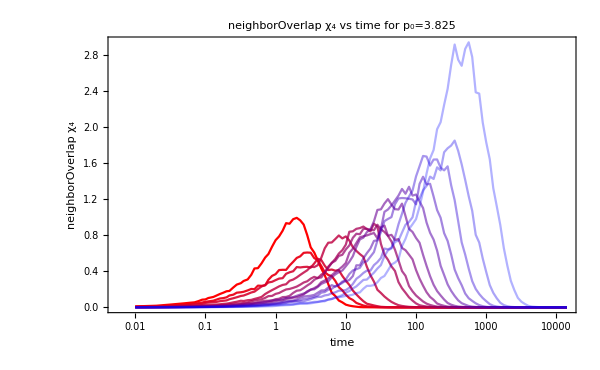

```mathematica
neighborOverlapPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],neighborOverlapVar[[p,T,rec]]*4096},{rec,Length[neighborOverlapVar[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","neighborOverlap χ_4"},ImageSize->600,PlotLabel->"neighborOverlap χ_4 vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,1}];
Column[neighborOverlapPlots]
```

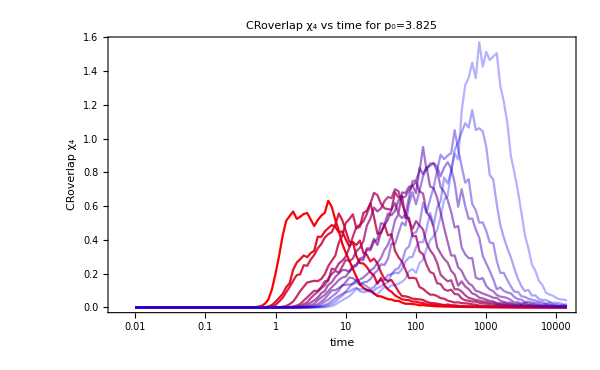

```mathematica
CRoverlapPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapVar[[p,T,rec]]*4096},{rec,Length[CRoverlapVar[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap χ_4"},ImageSize->600,PlotLabel->"CRoverlap χ_4 vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,1}];
Column[CRoverlapPlots]
```

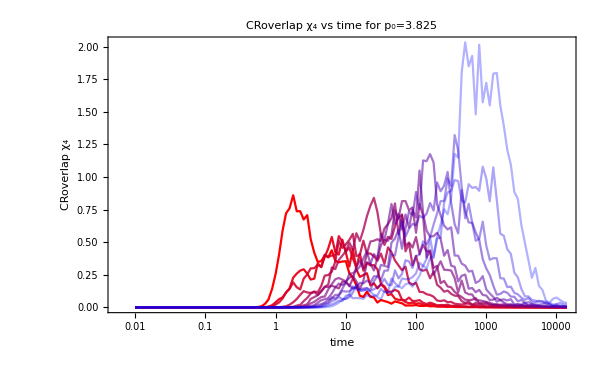

```mathematica
Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapVarSpacing5[[p,T,rec]]*4096},{rec,Length[CRoverlapVar[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap χ_4"},ImageSize->600,PlotLabel->"CRoverlap χ_4 vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,1}]
```

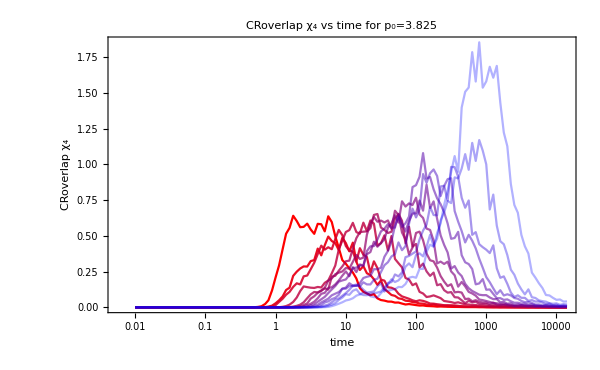

```mathematica
Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapVarSpacing2[[p,T,rec]]*4096},{rec,Length[CRoverlapVar[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap χ_4"},ImageSize->600,PlotLabel->"CRoverlap χ_4 vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,1}]
```

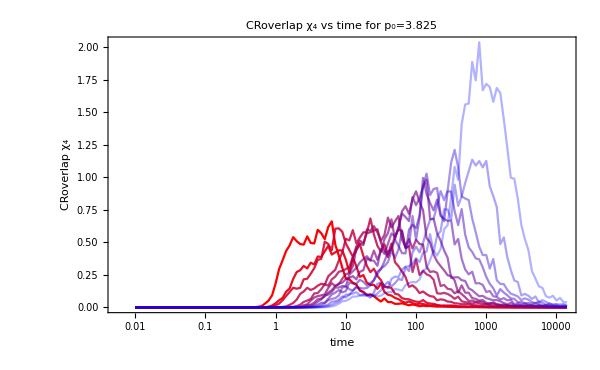

```mathematica
Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapVarSpacing3[[p,T,rec]]*4096},{rec,Length[CRoverlapVar[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap χ_4"},ImageSize->600,PlotLabel->"CRoverlap χ_4 vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,1}]
```

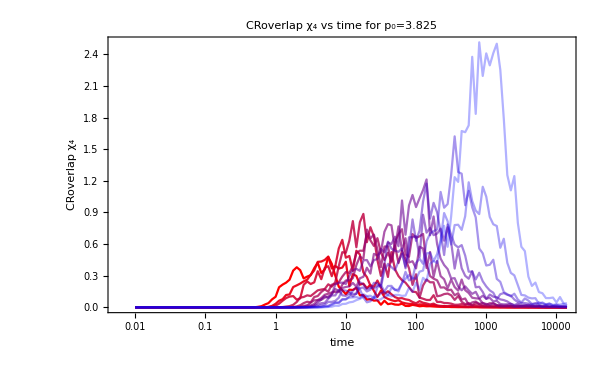

```mathematica
Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapVarSpacing9[[p,T,rec]]*4096},{rec,Length[CRoverlapVar[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap χ_4"},ImageSize->600,PlotLabel->"CRoverlap χ_4 vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,1}]
```

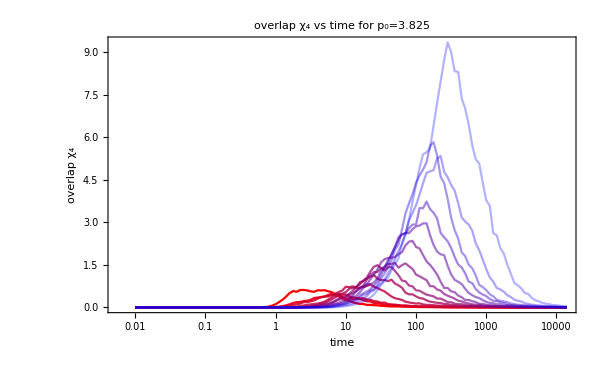

```mathematica
overlapPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],overlapVar[[p,T,rec]]*4096},{rec,Length[overlapVar[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","overlap χ_4"},ImageSize->600,PlotLabel->"overlap χ_4 vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,1}];
Column[overlapPlots]
```

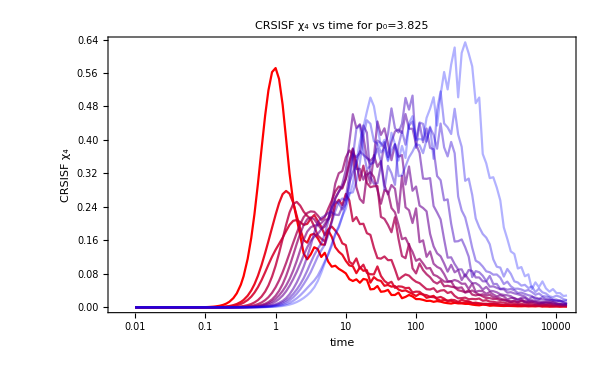

```mathematica
CRSISFPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRSISFVar[[p,T,rec]]*4096},{rec,Length[CRSISFVar[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF χ_4"},ImageSize->600,PlotLabel->"CRSISF χ_4 vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,1}];
Column[CRSISFPlots]
```

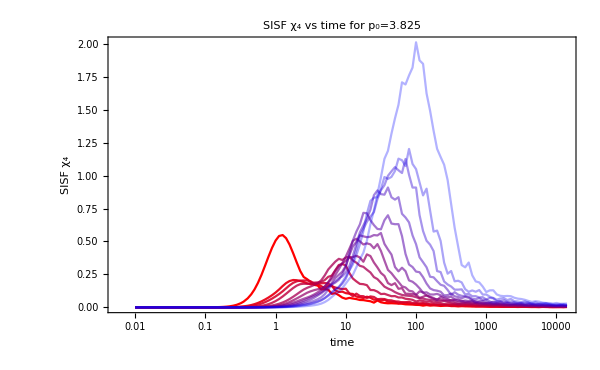

```mathematica
SISFPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],SISFVar[[p,T,rec]]*4096},{rec,Length[SISFVar[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","SISF χ_4"},ImageSize->600,PlotLabel->"SISF χ_4 vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,1}];
Column[SISFPlots]
```

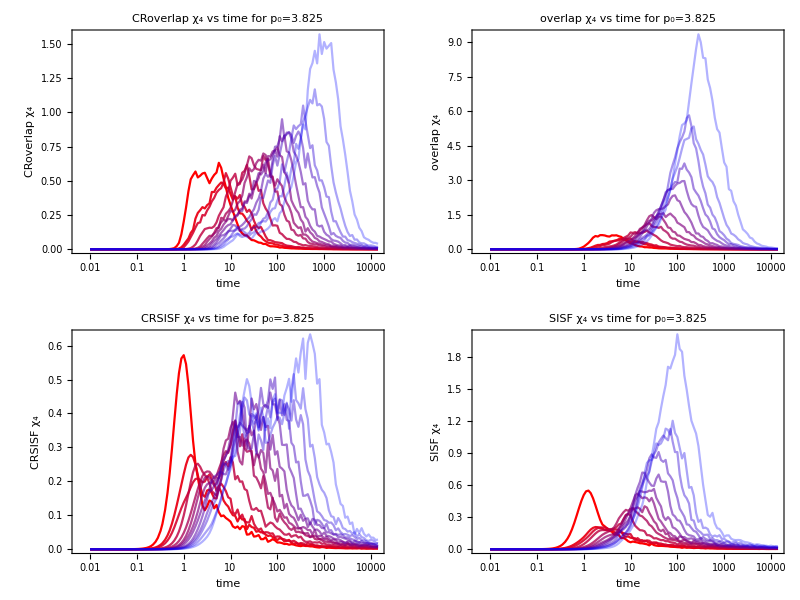

```mathematica
chi4Plots=Grid[Partition[{CRoverlapPlots[[1]],overlapPlots[[1]],CRSISFPlots[[1]],SISFPlots[[1]]},2]]
```

```mathematica
Export["/home/chengling/Research/updates/05022024/chi4.jpeg",chi4Plots,ImageResolution->800]
```

/home/chengling/Research/updates/05022024/chi4.jpeg

```mathematica
tauOverlapChi4={3.240281741034248,5.893621406466062,8.440263247078125,18.863267352285153,30.464154843193445,35.55407912412377,58.3942074597075,89.7090022629837,135.3965998844829,140.32918832607595,176.05486419287013,227.30754343144173,286.32620197032094};
```